## Tomography

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/alexanderpickston/Documents/GitHub/QIPmma/Tomography

```mathematica
Import[NotebookDirectory[]<>"library_quantumInformation.m"]
```

Set::write: Tag ColorData in ColorData[BlueGreenYellow] is Protected.

Running analysis using MATLink to combine the powers of mma with the powers of the cvx solver in matlab.

```mathematica
Needs["MATLink`"]
OpenMATLAB[]
```

## Package requirements

Note: Not necessary to run the tomography analysis—just previous functions that were used for getting analysis data ready to feed into the CVX solver.

### SDP tomography

```mathematica
probsPT[data_,order_]:=Flatten[(#//N)/Total[#]&/@(data[[#]]&/@order)][[Ordering[Flatten[order]]]] (* This sorts the data according to order, then normalizes and then inverts the sorting *)
normsPT[data_,order_]:=data/probsPT[data,order];
```

```mathematica
CoeffVec[nList_,pList_]:=√(nList/(pList(1-pList)))//N;
SOpState[nList_,pList_,meas_]:=Flatten/@(CoeffVec[nList,pList](ColVec[#*,Length[#]]&/@meas))//Chop;
SOpMeas[nList_,pList_,prep_]:=Flatten/@(CoeffVec[nList,pList](ColVec[#*,Length[#]]&/@prep))//Chop;
OptVec[nList_,pList_]:=List/@(pList*CoeffVec[nList,pList]);
```

```mathematica
(* Note: This takes density matrices as the input for measuredstates, not state vectors *)
MeasTomographyMAT[nList_List,pList_List,measuredstates_List(*density matrices*)]:=Module[{output,SDPFit},
SDPFit=MFunction["sdp_MeasTomo"];
output=SDPFit[
OptVec[N[nList],N[pList]],
SOpMeas[N[nList],N[pList],measuredstates]];
output];
```

```mathematica
StateTomographyMAT[nList_List,pList_List,measuredstates_List(*density matrices*)]:=Module[{output,SDPFit},
SDPFit=MFunction["sdp_StateTomo"];
output=SDPFit[
OptVec[N[nList],N[pList]],
SOpState[N[nList],N[pList],measuredstates]];
output];
```

## Testing tomo with MMA

For running any MATLAB specific syntax within mma need to write that syntax within MEvaluate[ ] . As an example magic(n) creates a matrix with random inputs that has dimensions n x n.

```mathematica
MEvaluate["mat = magic(4)"]
```

>> 
mat =

    16     2     3    13
     5    11    10     8
     9     7     6    12
     4    14    15     1

```mathematica
data=Import[NotebookDirectory[]<>"/currentImport.csv"];
```

Getting all the coincidences from the data set. This is in the form of a single list and will have to be partitioned later

```mathematica
cc=Flatten[data⟦2;;,-16;;⟧];
```

For creating strings with correct labels for all combinations of basis for all the combinations of different measurements.

```mathematica
DensityMatrixLabels[nQubits_]:= Tuples[{"H","V","D","A","R","L"},nQubits];
origin=DensityMatrixLabels[4];
ass = {z -> {"H","V"},x-> {"D","A"},y->{"R","L"}};
comb=Tuples[{z,x,y},4];
new = Flatten[ Tuples[#/.ass]&/@comb,1];
cyc=FindPermutation[origin,new];
```

List of all measurement settings.

```mathematica
3^4
```

81

Basis label now represents the measurements being made in terms of the actual vectors. The labeling/order of these measurement projections are crucial for the reconstruction and must map to the measurement order from the data set

```mathematica
basisVectors=Permute[Kron[Kron[Kron[{h,v,d,a,r,l},{h,v,d,a,r,l}],{h,v,d,a,r,l}],{h,v,d,a,r,l}],cyc];
```

```mathematica
input2=(Flatten[DensityMatrix[#]ᵀ])&/@basisVectors;
```

16 columns of coincidences. The initial import of the data is done so as a single list of all coincidences and we therefore need to split the data into lists of 16 coincidences based on the measurements made. This data structure should then be 81 lists of 16 values

```mathematica
Dimensions[Partition[cc,16]]
```

{81,16}

Finds the total number of n folds for each measurements and is therefore a list of 81 numbers

```mathematica
Total[Partition[cc,16],{2}];
N[Partition[cc,16]/Total[Partition[cc,16],{2}]];
```

```mathematica
input1=(List/@Flatten[N[Partition[cc,16]/Total[Partition[cc,16],{2}]]]);
Dimensions[input1]
```

{1296,1}

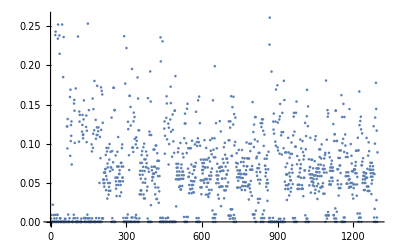

```mathematica
ListPlot[Flatten@input1]
```

```mathematica
Dimensions[input1]
```

{1296,1}

The list of input1 consists of now a single list of all of the measurement outcomes, partitioning this list now puts it back into its familiar form of 16 detection events corresponding to 81 measurements

```mathematica
Dimensions[Partition[input1,16]]
```

{81,16,1}

Understanding that input 2 is now a list of the density matrix form of the measurements (Z, Z, Z, Z) in vector form. The order of this list of vectors is again crucial. It must correspond to the recorded measurement settings.

```mathematica
{input2⟦1⟧==Flatten[DensityMatrix[Kron[h,h,h,h]]],
input2⟦2⟧==Flatten[DensityMatrix[Kron[h,h,h,v]]]}
Dimensions[input2]
```

{True,True}

{1296,256}

Calling the function from MATLAB using the MFunction[ ] capability. This then defines SDPFit[v, S] as a function which calls the MATLAB function which has the arguments:
S:    The (n x d) matrix corresponding to quadratic form
v:    vector measurements

In addition, a stylistic point to note here is that the labelling needs to be hard coded

```mathematica
DensityMatrixPlotLabels[nQubits_]:= Tuples[{"H","V"},nQubits];
```

```mathematica
labels=DensityMatrixPlotLabels[4];
labels=StringJoin/@labels;
labels=Framed[#,Background->Directive[LightGray,Opacity[.8]],FrameMargins->Tiny,FrameStyle->LightGray]&/@labels
```

{HHHH,HHHV,HHVH,HHVV,HVHH,HVHV,HVVH,HVVV,VHHH,VHHV,VHVH,VHVV,VVHH,VVHV,VVVH,VVVV}

```mathematica
DensityMatrixPlot[densitymatrx_]:=Show[BarChart3D[densitymatrx,

ChartLayout->"Grid",
ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"AuroraColors"],
BarSpacing->{.2,.2},
BaseStyle->{FontFamily->font,FontSize->fontSize,Black},
Method->{"Canvas"->None},
ChartBaseStyle->EdgeForm[{Thickness[.001],Opacity[1],Gray}],
Ticks->{Automatic,Automatic,dmticks},
Boxed->True,BoxStyle->{Directive[Thickness[0.001],Opacity[1],Gray,Dashed]},
FaceGrids->None,
Axes->{True,True,True},
AxesStyle->{Directive[Black,Opacity[0]],Directive[Black,Opacity[0]],Directive[Black]},
BoxRatios->{1,1,.6},
ImageSize->Large,
ViewPoint->{1.3,-2.4,2.},

ChartLabels->{{""},
Placed[labels,Axis,Rotate[#,-30*π/180]&],
Placed[labels,Axis,Rotate[#,Pi/4]&]},
LabelStyle->Directive[FontFamily->"IBM Plex Serif",FontSize->12]
]
]
```

```mathematica
SDPFit=MFunction["sdp_StateTomo"];
```

```mathematica
tomoMat=SDPFit[input1,input2];
```

```mathematica
{DensityMatrixPlot[Re[tomoMat]],DensityMatrixPlot[Im[tomoMat]]}
Purity[tomoMat]
```

{-Graphics3D-,-Graphics3D-}

0.834674+0. ⅈ

## Phase correction

```mathematica
purity[tomoMat]
```

0.855504

```mathematica
targetStatedm=#.#†&@((kron[h,h,v,h]+kron[v,v,h,v])/(√2));
```

```mathematica
phaseOp=kron[idn,idn,idn,({{1, 0}, {0, Exp[I ϕ]}})];
```

```mathematica
NMinimize[Re[TrNorm[
(targetStatedm-(kron[idn,idn,idn,({{1, 0}, {0, Exp[I ϕ]}})].tomoMat.kron[idn,idn,idn,({{1, 0}, {0, Exp[-I ϕ]}})]))]],ϕ,ϕ∈Reals]
```

```mathematica
TrNorm[phaseOp†.tomoMat.phaseOp]
```

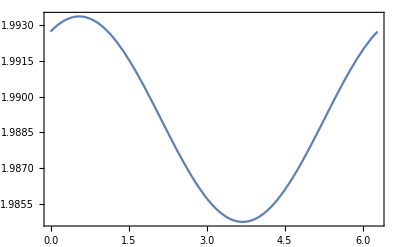

```mathematica
Plot[
Re[TrNorm[
Chop@(targetStatedm-(phaseOp†.tomoMat.phaseOp))]],{ϕ,0,2π}]
```

```mathematica
NMinimize[
{Re[TrNorm[
Chop@(targetStatedm-(phaseOp†.tomoMat.phaseOp))]],0≤ ϕ≤ 2Pi},ϕ]
```